# Implementing a LatticePlot function

Jack Heimrath (Mentor: Dariia Porechna)

## -Graphics-

GOAL OF THE PROJECT: A complete lattice is an additive subgroup of R^n that is isomorphic to Z^n. The goal of this project is to design a symbolic representation of arbitrary lattices of various dimensions in Wolfram Language and means to visualize tillings and filled vs empty cells to illustrate behavior of complicated systems like cellular automata.

SUMMARY OF RESULTS: 1. Implementation of a LatticePlot function which generates a 2 dimensional lattice with triangular, parallelogram, or hexagonal cells. Cell shapes can be specified by providing basis vectors.



2. Implementation of CAPlot and CAEvolution functions which generate Cellular Automata on the tillings made available with LatticePlot.

ADDITIONAL CONTENT:

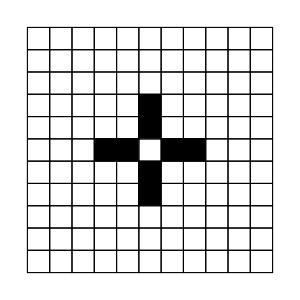
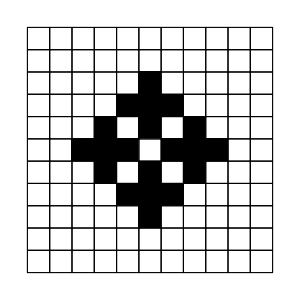
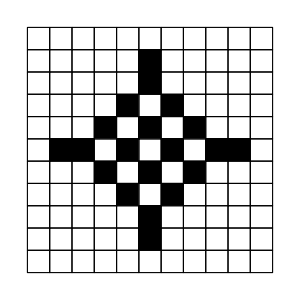
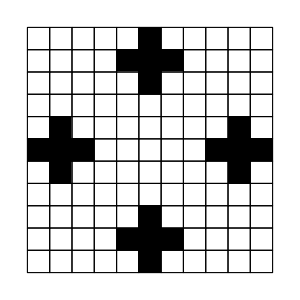
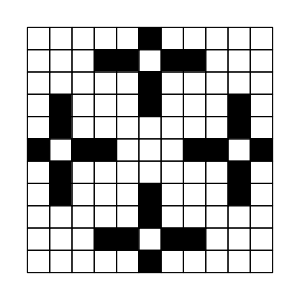
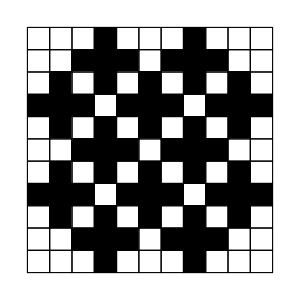
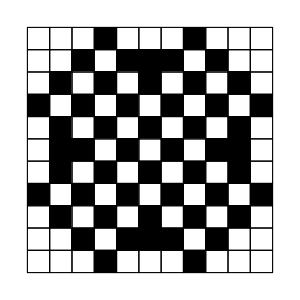
```mathematica
ListAnimate[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

FUTURE WORK: The most obvious next step is extending the new functions to work in 3 and more dimensions. Other possible ideas include the ability to choose between von Neumann (the current default) and Moore neighborhoods as well as procedural cell neighborhood detection (currently neighborhoods are hard coded). Finally, the CAPlot and CAEvolution functions take quite long to evaluate so it would be useful to find ways of making them run faster.